```mathematica
(*1. Selected project, created a directory and submited it to github.*)
```

```mathematica
(* 2. Introduction
(a) The syntax of the Mathematica language *)
```

```mathematica
{FullForm[a*b+c],FullForm[a+b*c]}
```

{Plus[Times[a,b],c],Plus[a,Times[b,c]]}

```mathematica
a*b+c//f
```

f[a b+c]

```mathematica
f@a*b+c
```

c+b f[a]

```mathematica
FullForm[a*(b+c)]
```

Times[a,Plus[b,c]]

```mathematica
∀_x∃_y x⊗y>y∧m ≠0⇒n⩾̸m
```

∀_x∃_y x⊗y>y&&m≠0⇒n⩾̸m

```mathematica
FullForm[%]
```

And[ForAll[x,Exists[y,Greater[CircleTimes[x,y],y]]],DoubleRightArrow[Unequal[m,0],NotGreaterSlantEqual[n,m]]]

```mathematica
{x -> #^2 &, (x -> #^2)&, x -> (#^2&)}
```

{x→#1^2&,x→#1^2&,x→(#1^2&)}

```mathematica
FullForm[a+b+c+d]
```

Plus[a,b,c,d]

```mathematica
FullForm[a^b^c^d]
```

Power[a,Power[b,Power[c,d]]]

```mathematica
a⊕b⊕c//FullForm
```

CirclePlus[a,b,c]

```mathematica
a×a×a×b×b×c
```

a^3 b^2 c

```mathematica
∫k[x]ⅆx//FullForm
```

Integrate[k[x],x]

```mathematica
∫a[x]b[x]ⅆx +c[x]
```

c[x]+∫a[x] b[x]ⅆx

```mathematica
x^(a+b)
```

x^(a+b)

```mathematica
D[x^n, x]
```

n x^(-1+n)

```mathematica
∑_(n=1)^∞ 1/n^s
```

Zeta[s]

```mathematica
∑_(n=1)^∞ 1/n^s+n
```

n+Zeta[s]

```mathematica
(*(b)The meaning of Expressions*)
```

```mathematica
(*meaning of             f meaning ofx,y...                 examples
Function                arguments or parameters              Sin[x],f[x,y]
Command                  arguments or parameters            Expand[(x+1)^2]
Operator                  operands                            x+y,a=b
Head                        elements                         {a,b,c}
Objecttype                  contents                      RGBColor[r,g,b]*)
```

```mathematica
(*(c)The Four Kinds of Bracketing in Mathematica*)
```

```mathematica
(*(term) parentheses for grouping
   f[x] square brackets for functions
  {a,b,c} curly braces for lists
  v[[i]] double brackets for indexing (Part[v,i])
 When the expressions you type in are complicated,it is often a good idea to put extra space inside each set of brackets.This makes it somewhat easier for you to see matching pairs of brackets.*)
```

```mathematica
(*(d) Use Brackets and Braces Correctly: *)
(*You use parentheses in Mathematica for grouping expressions and to determine the precedence of operations:*)
1+2/3
```

5/3

```mathematica
(1+2)/3
```

1

```mathematica
(*A list in Mathematica is represented by braces and is a collection of items referred to as elements.*)
(*Create a List of the first five positive integers:*)
{1,2,3,4,5}
```

{1,2,3,4,5}

```mathematica
{1,b,2,3,3x==12,√(9+y),"hello"}
```

```mathematica
{1,b,2,3,3 x==12,√(9+y),"hello"}
(*Lists can contain other lists to create nested lists:*)
{1,1,{3,4,5},{3,2}}
```

{1,b,2,3,3 x==12,√(9+y),hello}

{1,1,{3,4,5},{3,2}}

```mathematica
(*Square brackets are used in Mathematica to enclose the arguments of functions.*)
Range[10]
```

{1,2,3,4,5,6,7,8,9,10}

```mathematica
Sin[2]
```

Sin[2]

```mathematica
N[Sin[2]]
```

0.909297

```mathematica
(*Mathematica uses double square brackets as the short form for the Part function,which is used to get parts of lists:*)
v=Range[10]^2
```

{1,4,9,16,25,36,49,64,81,100}

```mathematica
v[[3]]
```

9

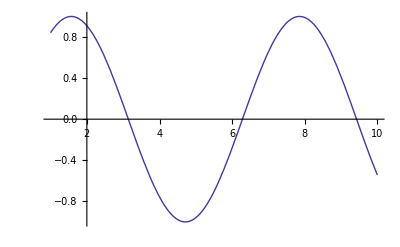

```mathematica
Plot[Sin[x],{x,1,10}]
```

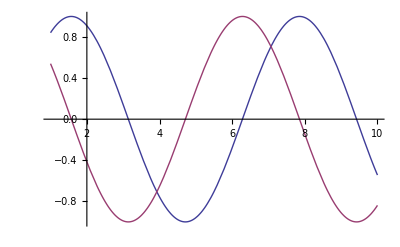

```mathematica
Plot[{Sin[x],Cos[x]},{x,1,10}]
```

```mathematica
(*All bracketing characters must be balanced for Mathematica to evaluate an expression.When a bracketing character is unbalanced,the Mathematica front end colors it purple and attempting to evaluate the expression produces an error*)
```